## Documentation

### Atlas Raw Data Structures

JSON / JLink -Xmx : http://reference.wolfram.com/mathematica/ref/message/Import/nojmem.html

atlas documentation : https://atlas.ripe.net/docs/data_struct 
RFC4950 ICMP Extensions for Multiprotocol Label Switching : http://tools.ietf.org/html/rfc4950
paris traceroute version : http://www.paris-traceroute.net

howto/AddErrorBarsToChartsAndPlots

### Data Source

```mathematica
ClearAll[fetchJSON];
fetchJSON[resultNumber_Integer, friendlyName_String]:=Block[
{defaultCacheDir, fullPathToCache,uri, jsonData},
defaultCacheDir=FileNameJoin[{NotebookDirectory[], "data"}];
fullPathToCache=FileNameJoin[{defaultCacheDir,"RIPE-Atlas-measurement-traceroute-"<>ToString[resultNumber]<>"-"<>friendlyName<>".json"}];
uri="https://atlas.ripe.net/api/v1/measurement/"<>ToString[resultNumber]<>"/result";

(* PREPARE JSON PARSER FOR LARGE FILES  *)
Needs["JLink`"];
UninstallJava[];
ReinstallJava[CommandLine->"java",JVMArguments->"-Xmx2024m"];

If[FileExistsQ[fullPathToCache],
jsonData=Import[fullPathToCache,"JSON"],
Module[{},
jsonData=Import[uri,"JSON"];
Export[fullPathToCache,fetchedSrc,"JSON"]];

(* CLEAN UP JSON PARSER *)
UninstallJava[];
(* --->RETURNING *)
jsonData
]
];
```

#### Read JSON file

```mathematica
(* 80mb JSON file *)
ClearAll[sampleJSONsrc];
sampleJSONSrc=fetchJSON[1608005,"digifortress"];
```

```mathematica
(* 20mb JSON file *)
ClearAll[tData];
tData=fetchJSON[1664934,"pacificEndpoint-Oahu"];
```

### Transcoding

#### Map Atlas JSON Traceroute To Summary

```mathematica
(* HST is -10 from GMT -- *)
unixTimeToHST[x_Integer]:=DateList[AbsoluteTime[{1970,1,1,2,0,0}]+x,TimeZone->-10];
(* TEST *)
unixTimeToHST[1399725833]
```

{2014,5,10,9,43,53.}

```mathematica
(* summarizeTestsInsideSingleHop : normalizes a single ping in the hop's interval test *)
ClearAll[summarizeTestsInsideSingleHop];
summarizeTestsInsideSingleHop::usage="summarizeTestsInsideSingleHop flattens out results - including optional results - into a standard format. This implies some of that optional info might well be dropped.  See normalizedResult::canonicalResult";
normalizedResult::canonicalResult="{from, rtt, size, ttl, errorsIfAny}";
(* MESSAGES *)
summarizeTestsInsideSingleHop::icmpnext="(opt) icmpnext chunk omitted";
summarizeTestsInsideSingleHop::unexpectedArg="`1`";
(* IMPLEMENTATION *) 
summarizeTestsInsideSingleHop[{"x"->"*"}]={"x"->"*"};
(* RESULT OKAY *)
summarizeTestsInsideSingleHop[{"from"->from_, "rtt" ->rtt_,"size"->size_Integer, "ttl"->ttl_Integer}]:= {from,rtt, size, ttl,{}};
(* ittl (optional) TimeToLive in packet that triggered the error ICMP. Omitted if equal to 1 (int) *)
summarizeTestsInsideSingleHop[{"from"->from_, "ittl"->ittl_Integer,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= {from,rtt, size,ttl,{"ittl"->ittl}};
(* late (optional) means the timeout exceed the wait time.  *)
summarizeTestsInsideSingleHop[{"from"->from_, "ittl"->ittl_Integer,"late" ->late_,"size"->size_, "ttl"->ttl_}]:= {from,ttl+1, size,ttl,{"late"->late}};
(* icmpext (optional)  *)
summarizeTestsInsideSingleHop[{"from"->from_, "icmpext"->icmpext_List,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= 
Block[{},
{from,rtt,size,ttl,{"icmpext"->icmpext}}];
summarizeTestsInsideSingleHop[{"from"->from_, "icmpext"->icmpext_List,"ittl"->ittl_Integer,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= 
Block[{},
{from,rtt,size,ttl,{"icmpext"->icmpext, "ittl"->ittl}}];
(* NOTIFY ON UNKNOWN ARGUMENT *) 
summarizeTestsInsideSingleHop [x_]:= Message[summarizeTestsInsideSingleHop::unexpectedArg,x];
(* TEST *)
atlasToComputableForm[sampleJSON[[3]]]//TableForm
```

prb_id→12735
proto→ICMP
paris_id→1
type→traceroute
interval→{{2014,5,10,9,45,7.},{2014,5,10,9,45,7.}}
proto→ICMP
hopsAsCDF→{{from→12735-10.0.1.1,min/mean/max→{0.396,0.475333,0.617},size→28,ttl→255,errorCount→0,timeouts→{}},{from→66.75.112.1,min/mean/max→{16.184,20.6163,24.6},size→28,ttl→254,errorCount→0,timeouts→{}},{from→24.25.231.25,min/mean/max→{8.858,9.836,11.353},size→28,ttl→253,errorCount→0,timeouts→{}},{from→72.129.45.3,min/mean/max→{10.168,10.45,10.931},size→40,ttl→252,errorCount→0,timeouts→{}}}

```mathematica
"result"/.tData[[95]]//TableForm
```

Need to handle the case where all time out - "hop"→1 | "result"→{{"x"→"*"},{"x"→"*"},{"x"→"*"}}

Need a time valued list of incidents when there was an outage (akin to the seismograph) to make clear when they occurred .  See

```mathematica
tracerouteWithTimeouts={{"af"->4,"dst_addr"->"72.129.45.3","dst_name"->"72.129.45.3","endtime"->1399737713,"from"->"24.94.68.214","fw"->4610,"group_id"->1664934,"msm_id"->1664934,"msm_name"->"Traceroute","paris_id"->14,"prb_id"->1178,"proto"->"ICMP","result"->{{"hop"->1,"result"->{{"x"->"*"},{"x"->"*"},{"x"->"*"}}},{"hop"->2,"result"->{{"from"->"24.25.230.137","rtt"->282.411,"size"->28,"ttl"->254},{"from"->"24.25.230.137","rtt"->251.608,"size"->28,"ttl"->254},{"from"->"24.25.230.137","rtt"->514.685,"size"->28,"ttl"->254}}},{"hop"->3,"result"->{{"from"->"72.129.45.68","rtt"->586.958,"size"->68,"ttl"->253},{"from"->"72.129.45.68","rtt"->71.773,"size"->68,"ttl"->253},{"from"->"72.129.45.68","rtt"->20.124,"size"->68,"ttl"->253}}},{"hop"->4,"result"->{{"from"->"72.129.45.52","rtt"->106.978,"size"->68,"ttl"->251},{"from"->"72.129.45.52","rtt"->107.174,"size"->68,"ttl"->251},{"from"->"72.129.45.52","rtt"->131.008,"size"->68,"ttl"->251}}},{"hop"->5,"result"->{{"from"->"72.129.45.0","rtt"->179.921,"size"->68,"ttl"->251},{"from"->"72.129.45.0","rtt"->184.114,"size"->68,"ttl"->251},{"from"->"72.129.45.0","rtt"->186.133,"size"->68,"ttl"->251}}},{"hop"->6,"result"->{{"from"->"66.75.161.48","rtt"->192.288,"size"->68,"ttl"->251},{"from"->"66.75.161.48","rtt"->190.946,"size"->68,"ttl"->251},{"from"->"66.75.161.48","rtt"->195.916,"size"->68,"ttl"->251}}},{"hop"->7,"result"->{{"from"->"72.129.45.3","rtt"->186.789,"size"->40,"ttl"->251},{"from"->"72.129.45.3","rtt"->184.689,"size"->40,"ttl"->251},{"from"->"72.129.45.3","rtt"->127.324,"size"->40,"ttl"->251}}}},"size"->40,"src_addr"->"192.168.5.228","timestamp"->1399737697,"type"->"traceroute"}};
```

```mathematica
atlasToComputableForm[tData[[95;;97]]]//TableForm
```

Part::take: Cannot take positions 95 through 97 in tData.

atlasToComputableForm[tData⟦95;;97⟧]

```mathematica
ClearAll[uniqueNonRoutable];
(* MESSAGES *)
uniqueNonRoutable::unexpectedArg="probeID->`1`, IPv4->`2`";
(* IMPLEMENTATION *)
uniqueNonRoutable["prb_id"->prbID_ ,ipV4_String/; StringMatchQ[ipV4,"192.168."~~___]]:=uniqueNonRoutable[prbID,ipV4]=ToString[prbID]<>"-"<>ipV4;
uniqueNonRoutable["prb_id"->prbID_ ,ipV4_String/; StringMatchQ[ipV4,"10."~~___]]:=uniqueNonRoutable[prbID,ipV4]=ToString[prbID]<>"-"<>ipV4;
uniqueNonRoutable["prb_id"->prbID_ ,ipV4_String/; StringMatchQ[ipV4,"172."~~Alternatives @@ToString /@Range[16,31]~~"."~~___]]:=uniqueNonRoutable[prbID,ipV4]=ToString[prbID]<>"-"<>ipV4;
uniqueNonRoutable["prb_id"->prbID_ ,ipV4_String]:=uniqueNonRoutable[prbID,ipV4]=ipV4;
(* NOTIFY ON UNKNOWN ARGUMENT *) 
uniqueNonRoutable[probeID_,ipV4_]:=Message[uniqueNonRoutable::unexpectedArg,"probeID->`1` IPv4->`2`"];
(* TEST *)
uniqueNonRoutable["prb_id"->"pxxxx", #]&/@{"192.168.100.1","10.100.100.1","172.16.0.1", "172.31.255.255","172.32.1.1"}//TableForm
```

pxxxx-192.168.100.1
pxxxx-10.100.100.1
pxxxx-172.16.0.1
pxxxx-172.31.255.255
172.32.1.1

```mathematica
(* summarizeHop : summarizes RTTs and errors from a specific hop in the traceroute for a probe *)
ClearAll[summarizeHop];
(* MESSAGES *)
summarizeHop::unexpectedArg="`1`";
(* IMPLEMENTATION *)
summarizeHop["prb_id"->prbID_,{"hop"->hopID_, "result"->testsInsideHop_List}]:= 
Block[{DEBUGargOnly=False},
If[DEBUGargOnly,testsInsideHop,
Block[
{errorFreeTests,erroredTests,allResultsAndTimeouts,allNormedResults ,whenDidTimeoutsHappen},
(* Exected form returned is {from, rtt, size, ttl, markAsErrorP, "errorDetails"->{(listOfRules}|{}) } *)
allResultsAndTimeouts=summarizeTestsInsideSingleHop /@ testsInsideHop;
(* Divide by timeouts versus results *)
whenDidTimeoutsHappen=Position[allResultsAndTimeouts,{"x"->"*"}];
allNormedResults=DeleteCases[allResultsAndTimeouts,{"x"->"*"}];
(* classifiy all non-timeout results *)
erroredTests=Cases[allNormedResults,{_,_,_,_,Length[_]>0}];
errorFreeTests=Cases[allNormedResults,{_,_,_,_,_}];
(* assert - the following values should always be the same during the interval test *)
(* TODO - IF TTL and SIZE do change during interval testing, is that indicitive of an error?  *)
(* returning... *)
If[allNormedResults≠ {},
Block[{firstResult,from, size, ttl, errorFreeRTTs, errorCount},
firstResult=allNormedResults[[1]];
from=firstResult[[1]];
size=firstResult[[3]];
ttl=firstResult[[4]];
errorFreeRTTs=If[Length[errorFreeTests]>0, errorFreeTests[[All,2]],{0,0}];
(* process erroredResults *)
errorCount=Length[erroredTests];
{"from"->uniqueNonRoutable["prb_id"-> prbID, from], "min/mean/max"->{Min[errorFreeRTTs],Mean[errorFreeRTTs], Max[errorFreeRTTs]}, "size"->size,"ttl"->ttl, "errorCount"->errorCount,"timeouts"->whenDidTimeoutsHappen}],
{"from"->uniqueNonRoutable["prb_id"-> prbID, "timeout"], "min/mean/max"->{300,300, 300}, "size"->25,"ttl"->300, "errorCount"->0,"timeouts"->whenDidTimeoutsHappen}]
]]
];
(* NOTIFY ON UNKNOWN ARGUMENT *) 
summarizeHop[x_]:=Message[summarizeHop::unexpectedArg,x];
(* TEST *)
atlasToComputableForm[sampleJSON[[1]]]//TableForm
```

prb_id→10546
proto→ICMP
paris_id→1
type→traceroute
interval→{{2014,5,10,9,43,53.},{2014,5,10,9,43,54.}}
proto→ICMP
hopsAsCDF→{{from→10546-192.168.1.1,min/mean/max→{0.561,0.617333,0.683},size→68,ttl→64,errorCount→0,timeouts→{}},{from→70.95.176.1,min/mean/max→{23.54,27.7587,29.982},size→28,ttl→254,errorCount→0,timeouts→{}},{from→24.25.230.229,min/mean/max→{11.997,12.55,13.312},size→28,ttl→253,errorCount→0,timeouts→{}},{from→72.129.45.3,min/mean/max→{11.082,13.3547,15.036},size→40,ttl→252,errorCount→0,timeouts→{}}}

```mathematica
(* walkProbeTraceroute : summarizes an individual probe's traceroute *)
ClearAll[walkProbeTraceroute];
(* MESSAGES *)
walkProbeTraceroute::usage="walkProbeTraceroute works through the results";
walkProbeTraceroute::unexpectedArg="`1`";
(* IMPLEMENTATION *)
(* Assert : hop is dropped in the expectation walkProbeTraceroute is always called in traversal order of the list of hops *)
walkProbeTraceroute["prb_id"->prbID_,hopsInTraceroute_List]:= 
(* Summary roll-up results of entire traceroute path is applied here *)
Block[{DEBUGshowArgOnly=False},
If[DEBUGshowArgOnly,hopsInTraceroute,
summarizeHop["prb_id"->prbID,#]&/@ hopsInTraceroute]];
(* NOTIFY ON UNKNOWN ARGUMENT *) 
walkProbeTraceroute[x_]:=Message[walkProbeTraceroute::unexpectedArg,x];
(* TEST *)
atlasToComputableForm[sampleJSON[[{1,5}]]]//TableForm
```

prb_id→10546 | proto→ICMP | paris_id→1 | type→traceroute | interval→{{2014,5,10,9,43,53.},{2014,5,10,9,43,54.}} | proto→ICMP | hopsAsCDF→{{from→10546-192.168.1.1,min/mean/max→{0.561,0.617333,0.683},size→68,ttl→64,errorCount→0,timeouts→{}},{from→70.95.176.1,min/mean/max→{23.54,27.7587,29.982},size→28,ttl→254,errorCount→0,timeouts→{}},{from→24.25.230.229,min/mean/max→{11.997,12.55,13.312},size→28,ttl→253,errorCount→0,timeouts→{}},{from→72.129.45.3,min/mean/max→{11.082,13.3547,15.036},size→40,ttl→252,errorCount→0,timeouts→{}}}
prb_id→14720 | proto→ICMP | paris_id→1 | type→traceroute | interval→{{2014,5,10,9,47,6.},{2014,5,10,9,47,9.}} | proto→ICMP | hopsAsCDF→{{from→128.171.0.1,min/mean/max→{0.503,0.558667,0.664},size→28,ttl→255,errorCount→0,timeouts→{}},{from→128.171.213.14,min/mean/max→{0.965,1.01733,1.055},size→28,ttl→253,errorCount→0,timeouts→{}},{from→205.166.205.22,min/mean/max→{1.021,1.038,1.07},size→28,ttl→253,errorCount→0,timeouts→{}},{from→64.57.21.49,min/mean/max→{65.542,75.0423,93.999},size→28,ttl→251,errorCount→0,timeouts→{}},{from→198.32.134.83,min/mean/max→{65.699,68.3457,73.565},size→28,ttl→250,errorCount→0,timeouts→{}},{from→66.109.6.144,min/mean/max→{93.623,94.409,95.914},size→140,ttl→246,errorCount→0,timeouts→{}},{from→66.109.9.44,min/mean/max→{93.606,94.307,95.034},size→140,ttl→247,errorCount→0,timeouts→{}},{from→66.109.6.7,min/mean/max→{93.65,94.249,95.438},size→68,ttl→248,errorCount→0,timeouts→{}},{from→107.14.19.33,min/mean/max→{93.625,95.506,99.216},size→68,ttl→247,errorCount→0,timeouts→{}},{from→72.129.17.1,min/mean/max→{93.88,96.3913,97.679},size→68,ttl→246,errorCount→0,timeouts→{}},{from→72.129.17.5,min/mean/max→{97.545,97.7683,97.991},size→68,ttl→245,errorCount→0,timeouts→{}},{from→72.129.17.2,min/mean/max→{95.389,96.877,97.699},size→68,ttl→246,errorCount→0,timeouts→{}},{from→72.129.45.3,min/mean/max→{73.531,73.7173,73.901},size→40,ttl→249,errorCount→0,timeouts→{}}}

```mathematica
(* atlasToComputableForm : Initiates the walk of traceroute results *)
ClearAll[atlasToComputableForm];
atlasToComputableForm::usage="Summarizes results from all probes";

atlasToComputableForm[{af_Rule,dstAddr_Rule,dstName_Rule, endTime_Rule,from_Rule, "fw"->4610,groupID_Rule,msmID_Rule,msmName_Rule,parisID_Rule,prbID_Rule,proto_Rule,"result"->result_List,size_Rule,srcAddr_Rule,timeStamp_Rule,type_Rule}] :=
Block[{DEBUGshowResultOnly=False},
If[DEBUGshowResultOnly,walkProbeTraceroute[result],{
prbID,
proto,
parisID,
type,
"interval"->{unixTimeToHST["timestamp"/.timeStamp],
unixTimeToHST["endtime"/.endTime]}, 
proto,
"hopsAsCDF"->walkProbeTraceroute[prbID,result]}
]];
(* Generalize for a list *)
atlasToComputableForm[aList_List]:= atlasToComputableForm /@ aList;
(* TEST *)
atlasToComputableForm[sampleJSON[[{3,4}]]]//TableForm
```

prb_id→12735 | proto→ICMP | paris_id→1 | type→traceroute | interval→{{2014,5,10,9,45,7.},{2014,5,10,9,45,7.}} | proto→ICMP | hopsAsCDF→{{from→12735-10.0.1.1,min/mean/max→{0.396,0.475333,0.617},size→28,ttl→255,errorCount→0,timeouts→{}},{from→66.75.112.1,min/mean/max→{16.184,20.6163,24.6},size→28,ttl→254,errorCount→0,timeouts→{}},{from→24.25.231.25,min/mean/max→{8.858,9.836,11.353},size→28,ttl→253,errorCount→0,timeouts→{}},{from→72.129.45.3,min/mean/max→{10.168,10.45,10.931},size→40,ttl→252,errorCount→0,timeouts→{}}}
prb_id→1178 | proto→ICMP | paris_id→1 | type→traceroute | interval→{{2014,5,10,9,46,25.},{2014,5,10,9,46,26.}} | proto→ICMP | hopsAsCDF→{{from→24.94.68.1,min/mean/max→{27.899,28.2573,28.45},size→28,ttl→255,errorCount→0,timeouts→{}},{from→24.25.230.137,min/mean/max→{16.311,21.7453,32.278},size→28,ttl→254,errorCount→0,timeouts→{}},{from→72.129.45.68,min/mean/max→{14.524,16.3823,18.212},size→68,ttl→253,errorCount→0,timeouts→{}},{from→72.129.45.52,min/mean/max→{17.98,18.803,20.36},size→68,ttl→251,errorCount→0,timeouts→{}},{from→72.129.45.0,min/mean/max→{68.115,68.322,68.488},size→68,ttl→251,errorCount→0,timeouts→{}},{from→66.75.161.48,min/mean/max→{68.44,69.815,70.708},size→68,ttl→251,errorCount→0,timeouts→{}},{from→72.129.45.3,min/mean/max→{66.755,69.3303,71.401},size→40,ttl→251,errorCount→0,timeouts→{}}}

```mathematica
(* pathsOnly extracts the unique traceroute path from all tests *)
ClearAll[pathOnly];
pathOnly::usage="Given a JSON traceroute list, distill down to the unique set of traceroute paths";
pathOnly::unexpectedArg="`1`";
(* IMPLEMENTATION *)
pathOnly[{"prb_id"->prbID_Integer,"proto"->proto_String,"paris_id"->parisID_Integer,"type"->type_String,"interval"->interval_List, "proto"->proto_String, "hopsAsCDF"->hopsAsCDF_List}]:= {
Block[{},
Flatten[{prbID,"from"/. # &/@hopsAsCDF[[All,1]]}]]
};
pathOnly[aList_List]:= Flatten[pathOnly/@ aList,1];
(* NOTIFY ON UNKNOWN ARGUMENT *) 
pathOnly[x_]:=Message[pathOnly::unexpectedArg,x];
(* TEST *)
pathOnly[atlasToComputableForm[sampleJSON[[{3,4}]]]]//MatrixForm
```

({12735,12735-10.0.1.1,66.75.112.1,24.25.231.25,72.129.45.3}
{1178,24.94.68.1,24.25.230.137,72.129.45.68,72.129.45.52,72.129.45.0,66.75.161.48,72.129.45.3})

```mathematica
Partition[#,2,1]&/@pathOnly[atlasToComputableForm[sampleJSON[[{3,4}]]]]//MatrixForm
```

({{12735,12735-10.0.1.1},{12735-10.0.1.1,66.75.112.1},{66.75.112.1,24.25.231.25},{24.25.231.25,72.129.45.3}}
{{1178,24.94.68.1},{24.94.68.1,24.25.230.137},{24.25.230.137,72.129.45.68},{72.129.45.68,72.129.45.52},{72.129.45.52,72.129.45.0},{72.129.45.0,66.75.161.48},{66.75.161.48,72.129.45.3}})

```mathematica
Apply[Rule,Partition[#,2,1]&/@pathOnly[atlasToComputableForm[sampleJSON[[{3,4}]]]],{2}]//MatrixForm
```

({12735→12735-10.0.1.1,12735-10.0.1.1→66.75.112.1,66.75.112.1→24.25.231.25,24.25.231.25→72.129.45.3}
{1178→24.94.68.1,24.94.68.1→24.25.230.137,24.25.230.137→72.129.45.68,72.129.45.68→72.129.45.52,72.129.45.52→72.129.45.0,72.129.45.0→66.75.161.48,66.75.161.48→72.129.45.3})

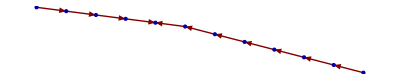

```mathematica
GraphPlot[Flatten[Apply[Rule,Partition[#,2,1]&/@pathOnly[atlasToComputableForm[sampleJSON[[{3,4}]]]],{2}],1], MultiedgeStyle->True, DirectedEdges->True, VertexLabeling->False]
```

```mathematica
traceroutesAsGraphPlot[jsonData_List]:=GraphPlot[Flatten[DeleteDuplicates[Apply[Rule,Partition[#,2,1]&/@pathOnly[atlasToComputableForm[jsonData]],{2}]],1], MultiedgeStyle->True, DirectedEdges->True, VertexLabeling->True];
```

summarizeTestsInsideSingleHop::unexpectedArg: {"x" → "*"}

summarizeTestsInsideSingleHop::unexpectedArg: {"from" → "24.94.68.1", "ittl" → 0, "late" → 2, "size" → 28, "ttl" → 254}

General::stop: Further output of summarizeTestsInsideSingleHop :: unexpectedArg will be suppressed during this calculation.

Part::partd: Part specification Null ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification Null ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification Null ⟦ 4 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

StringForm::sfr: Item 2 requested in ""probeID->\[NoBreak]`1`\[NoBreak], IPv4->\[NoBreak]`2`\[NoBreak]"" out of range; 1 items available.

uniqueNonRoutable::unexpectedArg: probeID->"probeID->`1` IPv4->`2`", IPv4->`2`

StringForm::sfr: Item 2 requested in ""probeID->\[NoBreak]`1`\[NoBreak], IPv4->\[NoBreak]`2`\[NoBreak]"" out of range; 1 items available.

uniqueNonRoutable::unexpectedArg: probeID->"probeID->`1` IPv4->`2`", IPv4->`2`

StringForm::sfr: Item 2 requested in ""probeID->\[NoBreak]`1`\[NoBreak], IPv4->\[NoBreak]`2`\[NoBreak]"" out of range; 1 items available.

General::stop: Further output of StringForm :: sfr will be suppressed during this calculation.

uniqueNonRoutable::unexpectedArg: probeID->"probeID->`1` IPv4->`2`", IPv4->`2`

General::stop: Further output of uniqueNonRoutable :: unexpectedArg will be suppressed during this calculation.

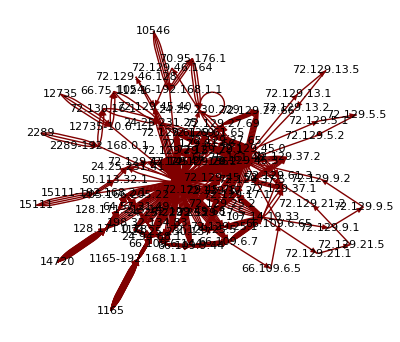

```mathematica
traceroutesAsGraphPlot[tData]
```

### Scratch

#### Extracting values from nested rules in JSON data

http://mathematica.stackexchange.com/questions/3111/extracting-values-from-nested-rules-in-json-data

```mathematica
tData=Import["https://atlas.ripe.net/api/v1/measurement/1664934/result/","JSON"];
```

```mathematica
tDataCDF=atlasToComputableForm[tData]
```

summarizeTestsInsideSingleHop::unexpectedArg: {"x" → "*"}

summarizeTestsInsideSingleHop::unexpectedArg: {"from" → "24.94.68.1", "ittl" → 0, "late" → 2, "size" → 28, "ttl" → 254}

General::stop: Further output of summarizeTestsInsideSingleHop :: unexpectedArg will be suppressed during this calculation.

Part::partd: Part specification Null ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification Null ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification Null ⟦ 4 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

StringForm::sfr: Item 2 requested in ""probeID->\[NoBreak]`1`\[NoBreak], IPv4->\[NoBreak]`2`\[NoBreak]"" out of range; 1 items available.

uniqueNonRoutable::unexpectedArg: probeID->"probeID->`1` IPv4->`2`", IPv4->`2`

StringForm::sfr: Item 2 requested in ""probeID->\[NoBreak]`1`\[NoBreak], IPv4->\[NoBreak]`2`\[NoBreak]"" out of range; 1 items available.

uniqueNonRoutable::unexpectedArg: probeID->"probeID->`1` IPv4->`2`", IPv4->`2`

StringForm::sfr: Item 2 requested in ""probeID->\[NoBreak]`1`\[NoBreak], IPv4->\[NoBreak]`2`\[NoBreak]"" out of range; 1 items available.

General::stop: Further output of StringForm :: sfr will be suppressed during this calculation.

uniqueNonRoutable::unexpectedArg: probeID->"probeID->`1` IPv4->`2`", IPv4->`2`

General::stop: Further output of uniqueNonRoutable :: unexpectedArg will be suppressed during this calculation.

{{prb_id→10546,proto→ICMP,paris_id→1,type→traceroute,interval→{{2014,5,10,9,43,53.},{2014,5,10,9,43,54.}},proto→ICMP,hopsAsCDF→{{from→10546-192.168.1.1,min/mean/max→{0.561,0.617333,0.683},size→68,ttl→64,errorCount→0,timeouts→{}},{from→70.95.176.1,min/mean/max→{23.54,27.7587,29.982},size→28,ttl→254,errorCount→0,timeouts→{}},{from→24.25.230.229,min/mean/max→{11.997,12.55,13.312},size→28,ttl→253,errorCount→0,timeouts→{}},{from→72.129.45.3,min/mean/max→{11.082,13.3547,15.036},size→40,ttl→252,errorCount→0,timeouts→{}}}},«8382»,{prb_id→2289,«5»,hopsAsCDF→{{from→2289-192.168.0.1,min/mean/max→{2.424,2.46933,2.519},size→68,ttl→64,errorCount→0,timeouts→{}},{from→72.130.16.1,min/mean/max→{17.719,30.4503,42.803},size→28,ttl→254,errorCount→0,timeouts→{}},{from→…,«4»,«1»},{from→72.129.45.3,min/mean/max→{13.337,15.1297,16.245},size→40,ttl→252,errorCount→0,timeouts→{}}}}}